```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define BWs

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;
```

## Charmonium

### Import Data

```mathematica
Tscanc={150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,194,197,200,204,207,210,213,216,218,221,224,227,230,234,237,240,243,246,249};
```

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

### Fitting

```mathematica
ccmodel=Range[1,Length[Tscanc]];
SetSharedVariable[ccmodel];
ParallelDo[Module[{n=ccmodel[[ii]],maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,ccdatac,bad},
maxx=Max[ccdata[n][[All,1]]];
minx=Min[ccdata[n][[All,1]]];
maxy=Max[ccdata[n][[All,2]]];
maxyx=ccdata[n][[Position[ccdata[n],Max[ccdata[n][[All,2]]]][[1,1]],1]];
maxyi=Position[ccdata[n][[All,1]],maxyx][[1,1]];
maxxy=ccdata[n][[Position[ccdata[n],Max[ccdata[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[ccdata[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
maxxis=Sort[Table[Position[ccdata[n][[All,1]],Nearest[ccdata[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
maxys=Table[ccdata[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
bad={};
Do[If[maxys[[i]]<maxys[[i+1]],bad=Append[bad,i]],{i,Length[maxys]-1}]
Do[maxxs=Delete[maxxs,bad[[i]]];maxys=Delete[maxys,bad[[i]]];maxxis=Delete[maxxis,bad[[i]]];,{i,Length[bad]}]
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[ccdata[n][[All,2]],Min[ccdata[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[ccdata[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[ccdata[n]]]];,
hwhmi=Position[ccdata[n],Nearest[ccdata[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[ccdata[n],Nearest[ccdata[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
Do[If[Or[2 ccdata[n][[hwhmi[[-i]],2]]≤0.5 maxys[[-i]],2 ccdata[n][[hwhmi[[-i]],2]]≥1.5 maxys[[-i]]],hwhmi[[-i]]=maxxis[[-i]]],{i,Length[hwhmi]-1}];
hwhmi=DeleteCases[maxxis-hwhmi,0];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-ccdata[n][[maxxis[[i]]-hwhmi[[i]],1]]),{i,Length[hwhmi]}];
ccdatac=Range[Length[maxxs]];
Do[ccdatac[[i]]=ccdata[n][[mins[[i]];;mins[[i+1]]]],{i,Length[maxxs]}];
ccmodel[[ii]]=Range[Length[hwhmi]];Do[ccmodel[[ii,i]]=NonlinearModelFit[ccdatac[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w],{i,Length[hwhmi]}];],{ii,Length[ccmodel]}]
```

### Results

```mathematica
ParallelDo[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];
If[Length[ccmodel[[i]]]>1,ccTcut=i],{i,Length[ccmodel]}];

wrfitcc=Range[Length[ccmodel]];
Do[wrfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[wrfitcc[[i,ii]]=wr/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[wrfitcc[[i]]]}],{i,Length[wrfitcc]}]

Γfitcc=Range[Length[ccmodel]];
Do[Γfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[Γfitcc[[i,ii]]=Γ/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[Γfitcc[[i]]]}],{i,Length[Γfitcc]}]

constfitcc=Range[Length[ccmodel]];
Do[constfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[constfitcc[[i,ii]]=const/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[constfitcc[[i]]]}],{i,Length[constfitcc]}]

areafitcc=Range[Length[ccmodel]];
Do[areafitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[areafitcc[[i,ii]]=π/2 constfitcc[[i,ii]] Γfitcc[[i,ii]],{ii,Length[areafitcc[[i]]]}],{i,Length[areafitcc]}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[ccmodel[[i,ii]][x],{x,0.7 wr/.ccmodel[[i,ii]]["BestFitParameters"],1.3 wr/.ccmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wr/.ccmodel[[i,ii]]["BestFitParameters"],Γ/.ccmodel[[i,ii]]["BestFitParameters"],const/.ccmodel[[i,ii]]["BestFitParameters"]],{x,0.7 wr/.ccmodel[[i,ii]]["BestFitParameters"],1.3 wr/.ccmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[ccmodel],1},{ii,1,Length[ccmodel[[1]]],1}]
```

```mathematica
ccTcut
```

19

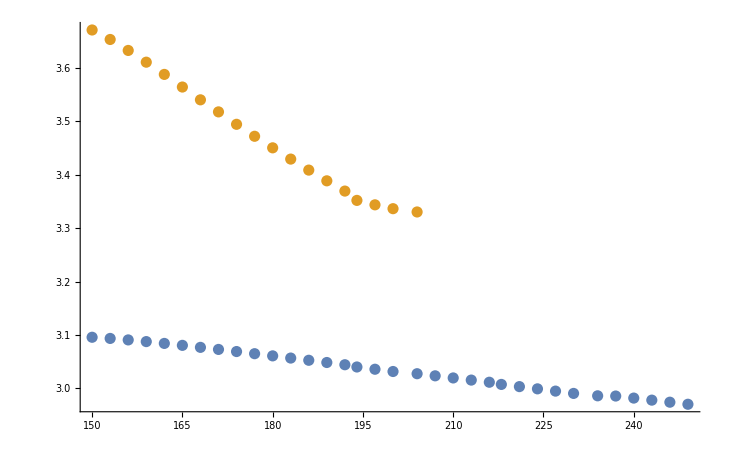

```mathematica
ListPlot[{Transpose[{Tscanc,wrfitcc[[All,1]]}],Transpose[{Tscanc[[;;ccTcut]],wrfitcc[[;;ccTcut,2]]}]}]
```

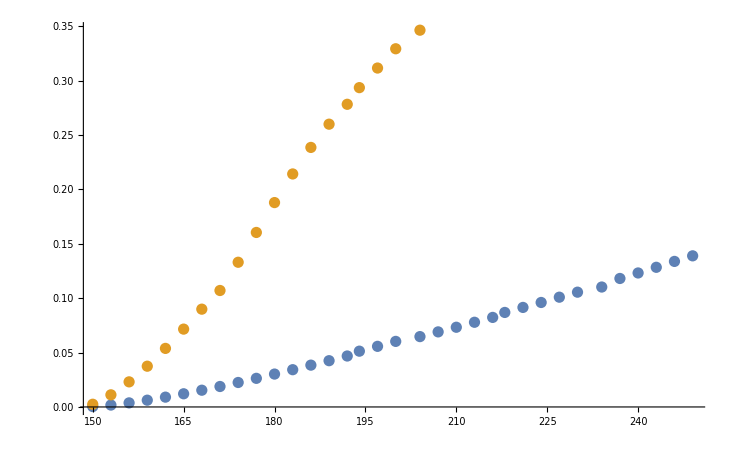

```mathematica
ListPlot[{Transpose[{Tscanc,Γfitcc[[All,1]]}],Transpose[{Tscanc[[;;ccTcut]],Γfitcc[[;;ccTcut,2]]}]}]
```

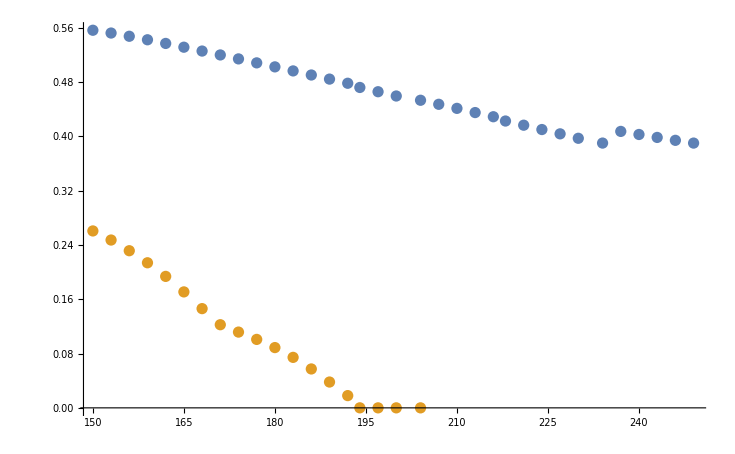

```mathematica
ListPlot[{Transpose[{Tscanc,areafitcc[[All,1]]}],Transpose[{Tscanc[[;;ccTcut]],areafitcc[[;;ccTcut,2]]}]}]
```

### Emission Rates

```mathematica
Emfactor=2.068897721078438;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,ccTcut];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,ccTcut}];
```

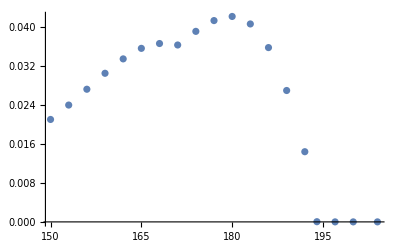

```mathematica
ListPlot[R0]
```

## Bottomonium

```mathematica
Do[bbdata[n]=Import["/Users/davidlafferty/Projects/master/spectraldata/swbbT"<>ToString[n]<>"spectra.dat"];,{n,7}];
Manipulate[ListPlot[bbdata[n],Joined->True],{n,2,7,1}]
```

### Fitting

```mathematica
bbmodel=Range[2,7];
Do[Module[{n=bbmodel[[ii]],maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,bbdatac},
maxx=Max[bbdata[n][[All,1]]];
minx=Min[bbdata[n][[All,1]]];
maxy=Max[bbdata[n][[All,2]]];
maxyx=bbdata[n][[Position[bbdata[n],Max[bbdata[n][[All,2]]]][[1,1]],1]];
maxyi=Position[bbdata[n][[All,1]],maxyx][[1,1]];
maxxy=bbdata[n][[Position[bbdata[n],Max[bbdata[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[bbdata[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/20}],First][[All,2]]]];
maxxis=Sort[Table[Position[bbdata[n][[All,1]],Nearest[bbdata[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
maxys=Table[bbdata[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[bbdata[n][[All,2]],Min[bbdata[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])];,
hwhmi=Position[bbdata[n],Nearest[bbdata[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[bbdata[n],Nearest[bbdata[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
Do[If[Or[2 bbdata[n][[hwhmi[[-i]],2]]≤0.5 maxys[[-i]],2 bbdata[n][[hwhmi[[-i]],2]]≥1.5 maxys[[-i]]],hwhmi[[-i]]=maxxis[[-i]]],{i,Length[hwhmi]-1}];
hwhmi=DeleteCases[maxxis-hwhmi,0];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-bbdata[n][[maxxis[[i]]-hwhmi[[i]],1]]),{i,Length[hwhmi]}];
bbdatac=Range[Length[maxxs]];
Do[bbdatac[[i]]=bbdata[n][[mins[[i]];;mins[[i+1]]]],{i,Length[maxxs]}];
bbmodel[[ii]]=Range[Length[hwhmi]];Do[bbmodel[[ii,i]]=NonlinearModelFit[bbdatac[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w],{i,Length[hwhmi]}];],{ii,Length[bbmodel]}]
```

### Results

```mathematica
wrfitbb=Range[Length[bbmodel]];
Do[wrfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[wrfitbb[[i,ii]]=wr/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[wrfitbb[[i]]]}],{i,Length[wrfitbb]}]

Γfitbb=Range[Length[bbmodel]];
Do[Γfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[Γfitbb[[i,ii]]=Γ/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[Γfitbb[[i]]]}],{i,Length[Γfitbb]}]

constfitbb=Range[Length[bbmodel]];
Do[constfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[constfitbb[[i,ii]]=const/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[constfitbb[[i]]]}],{i,Length[constfitbb]}]

areafitbb=Range[Length[bbmodel]];
Do[areafitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[areafitbb[[i,ii]]=π/2 constfitbb[[i,ii]] Γfitbb[[i,ii]],{ii,Length[areafitbb[[i]]]}],{i,Length[areafitbb]}]
```

```mathematica
Manipulate[Show[{ListPlot[bbdata[i+1],Joined->True],Plot[bbmodel[[i,ii]][x],{x,0.7 wr/.bbmodel[[i,ii]]["BestFitParameters"],1.3 wr/.bbmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wr/.bbmodel[[i,ii]]["BestFitParameters"],Γ/.bbmodel[[i,ii]]["BestFitParameters"],const/.bbmodel[[i,ii]]["BestFitParameters"]],{x,0.7 wr/.bbmodel[[i,ii]]["BestFitParameters"],1.3 wr/.bbmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[bbmodel],1},{ii,1,Length[bbmodel[[1]]],1}]
```